```mathematica
f[x_]:=Cos[2 Pi x]
range={-2, 2, 100};
```

```mathematica
sincn[x_]:=N[Sin[Pi x]/(Pi x)]
```

```mathematica
r1=range[[1]];r2=range[[2]];NP=range[[3]];
sr1=-10;sr2=10;T=N[(r2-r1)/NP];
Sx=Range[r1, r2, T];
Sy=f/@Sx;
```

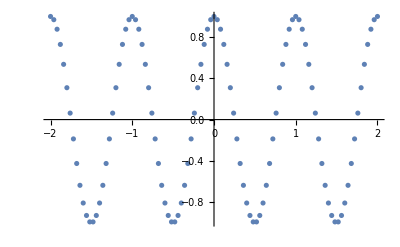

```mathematica
ListPlot[Transpose[{Sx, Sy}]]
```

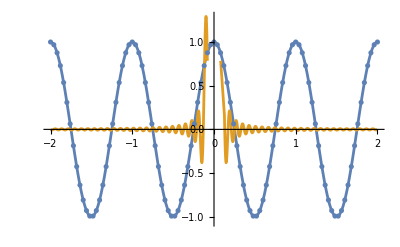

```mathematica
cft4[S_][t_]:=S.(sincn[(t-# T)/T ]&/@Sx)
Show[Plot[{f[x], cft4[Sy][x]}, {x, r1, r2}], ListPlot[Transpose[{Sx, Sy}]]]
```